```mathematica
NS["plots_talk_190516","C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
f2=Flatten@Import["talk_4mom_prior2_N10000.csv"];f2[[;;3]]
```

{2.4×10^-6,3.31×10^-6,4.53×10^-6}

```mathematica
f20=Flatten@Import["talk_4mom_priorn_N10000.csv"];f20[[;;3]]
```

{2.46×10^-6,3.39×10^-6,4.63×10^-6}

```mathematica
fs=Flatten@Import["stensola_activity_freqs_bins417641.csv"]
```

{0.497011,0.302466,0.127827,0.049794,0.0166195,0.0047457,0.00121396,0.00026099,0.0000550712,7.1832×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
{n=Length@fs-1,nn=Length@f2-1}
```

{65,10000}

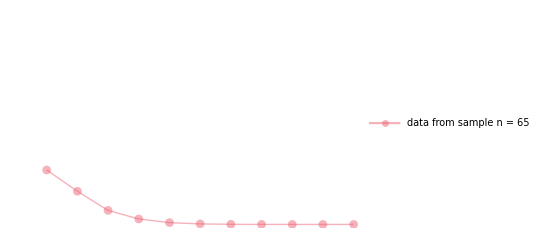

```mathematica
rg=0.15;plot=ListPlot[{fs[[;;Round[rg*n+1]]]*n,f2[[;;Round[rg*nn+1]]]*nn} ,Joined->True, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->{{solid,red,Opacity[0.5]},{solid,white,Opacity[0.0]}},
PlotLegends->Placed[{"data from sample n = 65"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_data",plot];
```

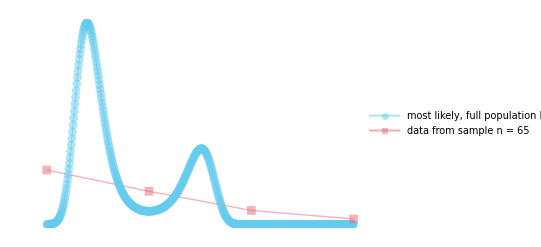

```mathematica
rg=0.05;
op=0.5;plot=ListPlot[{f2[[;;Round[rg*nn+1]]]*nn,fs[[;;Round[rg*n+1]]]*n} ,Joined->True, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->{{solid,blue,Opacity[op]},{solid,red,Opacity[op]}},
PlotLegends->Placed[{"most likely, full population N = 10000","data from sample n = 65"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_data_rg005_10000",plot];
```

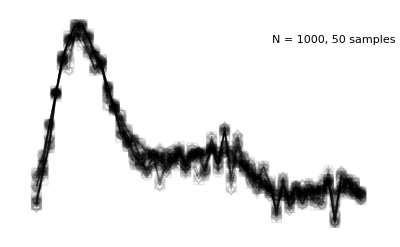

```mathematica
rg=0.05;plot=ListPlot[freqs[[;;50,;;Round[rg*1000+1]]]*1000 ,Joined->True, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->Directive[{solid,Black,Opacity[0.1]}],
(*PlotLegends->Placed[{"data, n = 65","full population, N = 10000"},{Right,Top}],*)
Epilog->Text["N = 1000, 50 samples",Scaled[{0.9,0.9}]],FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_MCsamples50_N1000",plot];
```

```mathematica
which="talk";prior="2";
n=65;
momx=4;
nnrange={n,1000,5000,10000};
rg=0.05;
distrs=Table[
T@{Range[0,nn]/nn*100,
If[nn==n,
fs*n,
Flatten@Import["stensola_"<>ToString[momx]<>"mom_prior"<>prior<>"_N"<>ToString[nn]<>".csv"]*nn]}
,{nn,Reverse@nnrange}];
op=0.5;
plot=ListPlot[distrs,Joined->True, PlotRange->{{All,rg*100},{All,All}},PlotMarkers->Auto,
PlotStyle->Reverse@{{solid,red,Opacity[op]},{solid,yellow,Opacity[op]},{solid,green,Opacity[op]},{solid,blue,Opacity[op]}},

(*PlotStyle->Directive[{solid,Opacity[0.5]}],*)PlotLegends->Placed[Reverse@Table[If[nn==n,"data from sample n = 65","most likely, full population N = "<>ToString[nn]],{nn,nnrange}],{Right,Top}],(*Epilog->Text[ToString[momx]<>" moments, prior "<>prior,Scaled[{0.9,0.1}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside];
expdf[which<>"_"<>ToString[momx]<>"mom_distributionsN_prior"<>prior,plot];
```

```mathematica
(* riehle *)
```

```mathematica
f2=Flatten@Import["riehle_6mom_prior2_N10000.csv"];f2[[;;3]]
```

{6.0811×10^-24,8.1534×10^-24,1.09181×10^-23}

```mathematica
fs=Flatten@Import["riehle_activity_freqs_bins300394.csv"];fs[[;;3]]
```

{0.000878846,0.00503672,0.0166881}

```mathematica
{n=Length@fs-1,nn=Length@f2-1}
```

{159,10000}

```mathematica
fr=2*Table[(1-aa+nn)/((nn+1)*(nn+2)),{aa,0,nn}];
Length@fr
```

10001

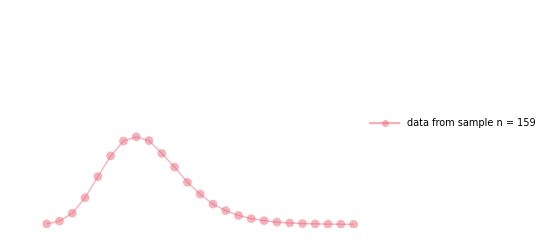

```mathematica
rg=0.15;plot=ListPlot[{fs[[;;Round[rg*n+1]]]*n,f2[[;;Round[rg*nn+1]]]*nn} ,Joined->True, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->{{solid,red,Opacity[0.5]},{solid,white,Opacity[0.0]}},
PlotLegends->Placed[{"data from sample n = 159"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_data_riehle",plot];
```

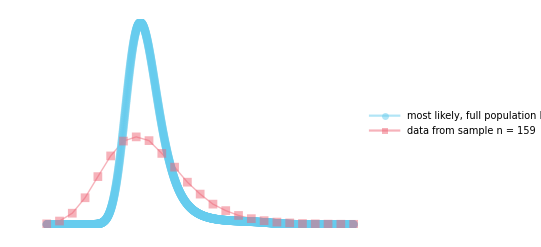

```mathematica
rg=0.15;
op=0.5;plot=ListPlot[{f2[[;;Round[rg*nn+1]]]*nn,fs[[;;Round[rg*n+1]]]*n} ,Joined->True, PlotRange->{All,All},DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->{{solid,blue,Opacity[op]},{solid,red,Opacity[op]}},
PlotLegends->Placed[{"most likely, full population N = 10000","data from sample n = 159"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_data_riehle_rg015_10000",plot];
```

```mathematica
(* pre-data *)
```

```mathematica
fr=2*Table[(1-aa+nn)/((nn+1)*(nn+2)),{aa,0,nn}];
fr0=N[(#/Total@#)&@Table[Binomial[nn,aa],{aa,0,nn}]];
frn=(#/Total@#)&@Table[PDF[NormalDistribution[0.03*nn,0.04*nn],aa],{aa,0,nn}];
```

```mathematica
Total[fr0]
```

1.

```mathematica
fr0[[;;5]]
```

{0.,0.,0.,0.,0.}

```mathematica
rg=0.05;
op=0.1;plot=ListPlot[{fr,frn}*nn ,Joined->True, PlotRange->{All,{All,All}},DataRange->{0,1}*100,PlotMarkers->Auto,PlotStyle->{{solid,blue,Opacity[op]},{solid,yellow,Opacity[op]}},
PlotLegends->Placed[{"sensible pre-data belief", "normal pre-data belief, N = 10000"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside];
expdf["talk_priorsn_10000",plot];
```

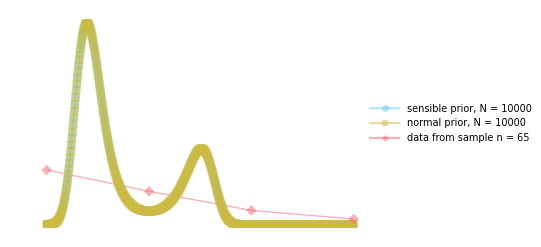

```mathematica
rg=0.05;
op=0.5;plot=ListPlot[{f2[[;;Round[rg*nn+1]]]*nn,f20[[;;Round[rg*nn+1]]]*nn,fs[[;;Round[rg*n+1]]]*n} ,Joined->True, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->Auto,PlotStyle->{{solid,blue,Opacity[op]},{solid,yellow,Opacity[op]},{solid,red,Opacity[op]}},
PlotLegends->Placed[{"sensible prior, N = 10000","normal prior, N = 10000","data from sample n = 65"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside]
```

```mathematica
expdf["talk_data_priors_rg005_10000",plot];
```

```mathematica
(* load scripts to calculate the Lagrange multipliers from the constraints, sensible prior *)
<<"ME_1fmoms.m";
```

```mathematica
(* NOTE: max discrepancy between recovered moments in the calculation below has been 0.0001% *)
```

```mathematica
nnrange={10000};
```

```mathematica
(* stensola, 2 moments *)
n=65;
nmom=4;moments=(Flatten@Import["stensola_norm_allbinomeans.csv"])[[;;nmom]]
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
Do[Print[nn];
{js,distr,norm2}=ME1fmomsn[Rationalize[moments,0],nn,12];
Export["talk_"<>ToString[nmom]<>"mom_priorn_N"<>ToString[nn]<>".csv",{distr}];
,{nn,Flatten@{nnrange}}];
```

```mathematica
fex=(#/Total@#)&@Table[PDF[NormalDistribution[0.03*nn,0.04*nn],aa],{aa,0,nn}];
```

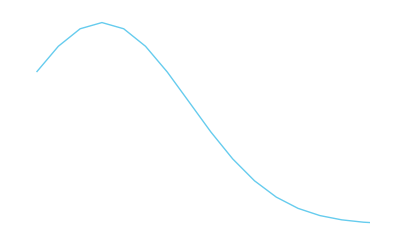

```mathematica
ListPlot[fex[[;;;;Round[nn/100]]],PlotRange->{{All,15},All},Joined->True,DataRange->{0,100}]
```

```mathematica
PDF[NormalDistribution[3/100*nn,4/100*nn],aa]
```

(ⅇ^(-(-300+aa)^2/320000))/(400 √(2 π))

```mathematica
gm[a_]:=gm[a]=Table[Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa],{aa,0,nn}];
```

```mathematica
gm0=gm[0];
```

```mathematica
rg=0.15;
op=0.5;plot=ListPlot[{f2[[;;Round[rg*nn+1]]]*nn,fs[[;;Round[rg*n+1]]]*n,gm[0][[;;Round[rg*nn+1]]]*n,gm[1][[;;Round[rg*nn+1]]]*n,gm[2][[;;Round[rg*nn+1]]]*n} ,Joined->{False,False,True,True,True}, PlotRange->All,DataRange->{0,rg}*100,PlotMarkers->{{●,10},{■,25},{○,0},{○,0},{○,0}},PlotStyle->{{solid,blue,Opacity[op]},{solid,red,Opacity[op]},{Dashing[{0.01,0.01}],yellow,Opacity[op]},{Dashing[{0.01,0.01}],yellow,Opacity[op]},{Dashing[{0.01,0.01}],yellow,Opacity[op]}},
PlotLegends->Placed[{"most likely, full population N = 10000","data from sample n = 65"},{Right,Top}],(*Epilog->Text["n = "<>ToString[n],Scaled[{0.9,0.5}]],*)FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside];
expdf["talk_window0",plot];
```